Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}
];
```

```mathematica
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
```

```mathematica
Simplify[sigtheta/.r->ri]
```

(-2 PO re^2+PI (re^2+ri^2))/(re^2-ri^2)

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=-nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning
];
```

Dado dint, dext e dT, calcula a TA devido à temperatura

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=12.42 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature
]
```

Calcula-se o alongamento equivalente e a reação de apoio

```mathematica
(*ComputeAxialReaction[Force_,de_,di_]:=Block[{tabf,df,n=1000,DL,DF,young = 3 10^7,area,L=1},
area=Pi/4(de^2 -di^2);
df=Force/n;
tabf=Table[Force-df i,{i,1,n}];
PrependTo[tabf,Force];
DL=1/ (young area) Sum[tabf[[i]] (L/n),{i,1,n}];
DF=young DL/L  area;
DF
];*)
```

```mathematica
ComputeAxialReaction[Force_,area_,L_]:=Block[{tabf,df,Steps=1000,DL,DF,young =3 10^7,dx,x,w,i},
dx=L/Steps;
DL=0.;
x=0.;
w=Force/L;
For[i=1,i≤Steps,i++,
DL+=w(2 x dx+dx^2)/2;
x+=dx;
]; 
DL=DL/(young area);
(*Print["DL = ",DL];*)
DF=young DL/L  area
];
R=0;
w=3;
stepss=10;
dx=9/stepss;
f=0;
x=0.;
area=0.1 0.2;
For[jj=1,jj≤stepss,jj++,
f=w dx;
R+=ComputeAxialReaction[f,area,dx];
f=x w;
x+=dx;
];
R
```

```mathematica
ComputeReaction[Force_,area_,L_]:=Block[{tabf,df,DL,DF,young =3 10^7,dx,x,w,i},
w=Force/L;
DL=w L^2/(2 young area);
young DL/L  area
];
```

```mathematica
ComputeReaction[3 9,0.1 0.2,9]
```

13.5

```mathematica
ComputeBalooningFreePart[pipedatavec_,PiData_,PeData_,Lcement_]:=Block[{bal,pipe,de,di,i,ndata,L1,young,nu,weigthperfeet,L2,sigy},
bal=0;
pipe=1;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=pipedatavec[[pipe]];
ndata=Length[PiData];
For[i=ndata,i≥1,i--,
If[L1>PiData[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=pipedatavec[[pipe]];
];
If[PiData[[i,2]]<=Lcement,
bal+=ComputeFballoning[di,de,PiData[[i,1]],PeData[[i,2]],nu];
];
];
bal/ndata
]
```

Discretização do tubular(Comprimento e Pressão)

```mathematica
ExpandTable[table_,ntimes_]:=Block[{i,deltaL,deltaP,newtab={},j,pi,l,lastp=0,lastl=0,tol=10^-8},
For[j=2,j≤Length[table],j++,
deltaL=(table[[j,2]]-table[[j-1,2]])/ntimes;
deltaP=(table[[j,1]]-table[[j-1,1]])/ntimes;
If[deltaP<0.1,deltaP=0.1];
If[deltaL<0.1,deltaL=0.1];
pi=table[[j-1,1]];
l=table[[j-1,2]];
For[i=1,i≤ntimes,i++,

l+=deltaL;
pi+=deltaP;
If[(pi-lastp)>tol &&(l-lastl)>tol,
AppendTo[newtab,{pi,l}];
];
lastp=pi;
lastl=l;
];
];
newtab
]
```

Discretização do tubular(Pressão)

```mathematica
ExpandTableOne[table_,ntimes_]:=Block[{i,deltaL,deltaP,newtab={},j,pi,l},
For[j=2,j≤Length[table],j++,
deltaP=(table[[j]]-table[[j-1]])/ntimes;
pi=table[[j]];
For[i=1,i≤ntimes,i++,
AppendTo[newtab,pi];
pi+=deltaP;
];
];
newtab
]
```

Cortando o vetor no ponto desejado (lcut)

```mathematica
FilterData[data_,lcut_,topdown_]:=Block[{newdata={},i},
i=1;
If[topdown==1,
While[data[[i,2]]<=lcut,
AppendTo[newdata,data[[i,1]]];
i++;
];
,
i=Length[data];
While[data[[i,2]]>=lcut,
AppendTo[newdata,data[[i,1]]];
i--;
];

];
newdata
]
```

```mathematica
FilterData[data_,lcut_]:=Block[{newdata={},i},
i=1;
While[data[[i,2]]<=lcut,
AppendTo[newdata,data[[i,1]]];
i++;
];

newdata
]
```

Inverte a ordem do vetor(traz para frente e vice versa)

```mathematica
InvertOrder[ax_]:=Block[{newax,i},
newax=Table[0,{Length[ax]}];
For[i=1,i<Length[ax],i++,
newax[[i]]=ax[[Length[ax]-i]];
];
newax[[Length[ax]]]=ax[[1]];
newax
];
```

Cálculo das pressões para o caso do poço cheio de gás

```mathematica
IntermediateKickLoadingFullOfGas[h_,LDA_,Linter_,Lnext_,Lcement_,globaldensitydata_,P0_]:=Block[{Psap,rhocement,sol,rhonext,rhogas,SurfacePressure,rhowater,hgas,hmud,Pib,Ptemp,hgi,Pob,eq1,eq2,ppgtopsi=0.051948,rhoHC,rhoPF},
{rhogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,SurfacePressure,Psap}=globaldensitydata;
(*P0=LDA rhowater ppgtopsi;*)
hmud=0;
hgas=Lnext;
Pib=Psap-ppgtopsi rhogas (Linter-h);
If[h>Lcement,
Pob=P0+ppgtopsi( rhowater (Lcement-LDA)+ rhocement (h-Lcement));
,
Pob=ppgtopsi rhowater (h-LDA)+P0;
];
{Pib,Pob}
];
```

Cálculo das pressões para o caso de um vazamento na coluna de produção

```mathematica
IntermediateTubingLeak[h_,LDA_,Lzpr_,Lcement_,globaldensitydata_]:=Block[{Pzpr,rhoPF,,Pcabpt,rhoHC,Psap,rhocement,sol,rhonext,rhogas,SurfacePressure,rhowater,hgas,hmud,Pib,Ptemp,hgi,Pob,P0,eq1,eq2,ppgtopsi=0.051948},
{rhogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,SurfacePressure,Pzpr}=globaldensitydata;
Pcabpt=Pzpr-ppgtopsi rhoHC (Lzpr-LDA);(*OK*)
P0=LDA rhowater  ppgtopsi;
Pib=Pcabpt+ppgtopsi rhoPF(h-LDA);
If[h>Lcement,
Pob=P0+ppgtopsi( rhowater (Lcement-LDA)+ rhocement (h-Lcement));
,
Pob=ppgtopsi rhowater (h-LDA)+P0;
];
{Pib,Pob}
];
```

Cálculo das pressões para o caso de perda de circulação

```mathematica
FullEvacIntermediate[h_,LDA_,Lnext_,globaldensitydata_]:=Block[{ha,hm1,hm2,ExtPress,InterPress,Linter,sz,hogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,P0,Psap,rhogas,Pib,Pob},
{rhogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,P0,Psap}=globaldensitydata;
InterPress=0;
ExtPress=P0+0.052 rhonext (h-LDA);
{InterPress,ExtPress}
];
```

```mathematica
SetData[currentpipedata_]:=Block[{de,di,t,sigy,young,nu,weigthft,nfactorStewart},
de=currentpipedata[[1]];
di=currentpipedata[[5]];
weigthft=currentpipedata[[2]];
t=currentpipedata[[4]];
sigy=currentpipedata[[13]];
young=currentpipedata[[11]];
nu=currentpipedata[[12]];
nfactorStewart=currentpipedata[[14]];
{de,di,t,sigy,young,nu,weigthft,nfactorStewart}
];
```

Cálculo das pressões ao longo do poço

```mathematica
ComputePressures[Lsap_,Lnext_,Lcement_,LDA_,PipesData_,globaldensitydata_,steps_,case_]:=Block[{npipes,PI={},PO={},i,j,Pib,Pob,counter,h,deltah,Lsection,currentpipedata,de,di,t,sigy,young,nu,weigthperfeet,n},
npipes=Length[PipesData];
h=Lsap;
For[i=npipes,i≥ 1,i--,
Lsection=PipesData[[i]][[2]]-PipesData[[i]][[1]];
deltah=Lsection/steps;
currentpipedata=PipesData[[i,3]];
{de,di,t,sigy,young,nu,weigthperfeet,n}=SetData[currentpipedata];

For[j=1 ,j≤steps,j++,
Switch[case,1,
P0=LDA 3.79 0.052;
{Pib,Pob}=IntermediateKickLoadingFullOfGas[h,LDA,Lsap,Lnext,Lcement,globaldensitydata,P0];
,2,
{Pib,Pob}=IntermediateTubingLeak[h,LDA,Lnext,Lcement,globaldensitydata];
,3,
{Pib,Pob}=FullEvacIntermediate[h,LDA,Lnext,globaldensitydata];
];
PrependTo[PI,{Pib,h/3.28}];
PrependTo[PO,{Pob,h/3.28}];
h-=deltah;
];

];
{PI,PO}
];
```

Cálculo da força pistão

```mathematica
ComputePistonForce[PiData_,PeData_,PipeData_]:=Block[{i,olddi,oldde,pipe,de,di,young,nu,weigthperfeet,L1,L2,PistonForce=0,sigy},
pipe=1;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
For[i=Length[PipeData],i>1,i--,
olddi=di;
oldde=de;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
PistonForce+=Pi/4 (olddi^2-di^2) PiData[[i,1]]-Pi/4 (oldde^2-de^2) PeData[[i,1]];
];
PistonForce
];
```

```mathematica
Barlow[sigy_,de_,di_]:=Block[{t=(de-di)/2},0.875 2 sigy/(de/t)]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt≥ range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}
];
```

Calcula a tensão de von Mises

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};
S=sig-1/3 Tr[sig] IdentityMatrix[3];
(*Print[S];*)
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

```mathematica
ComputeVonMises[sigrr ,sigtt,sigaa]//FullSimplify
```

√(sigaa^2+sigrr^2-sigrr sigtt+sigtt^2-sigaa (sigrr+sigtt))

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_]:=Block[{APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);
VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
barlow=Barlow[sigy,de,di];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
AppendTo[BarlowSF,{api[[1]]/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF}
];
```

Calcula a tensão axial

```mathematica
ComputeAxialStress[PiData_,PeData_,PipeData_,Lcement_,Ltotal_,Ti_,Tp_]:=Block[{deltabal,VecPicement,VecPecement,FPistn,FTempn,Fballoningn,Fballoningn1,AxialForceVec,WeigthFreePart,de,di,young,nu,weigthperfeet,BalloningForce=0,PistonForce=0,TemperatureForce=0,WeigthForce=0,dh=0,AxialForce={},ReactionForce=0,MeanPiFree=0,MeanPeFree=0,VecPi,VecPe,i,L1,L2,olddi,pipe,oldde,MeanTiFree,MeanTpFree,VecTi,VecTp,PistonForceJoints,sigy,PI,PO,Aint,Aext,OldAint,OldAext,ii,sumpi,sumpe,LDA=PiData[[1,2]],sumti,sumtp,PistTrue=False},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
pipe=1;
AxialForceVec=Table[0,{Length[PiData]},{2}];
For[i=Length[PiData]-1,i>1,i--,
PI= PiData[[i,1]];
PO= PeData[[i,1]];
Aint=Pi/4 di^2 ;
Aext=Pi/4 de^2 ;
(*No primeiro passo calcula o efeito pistão de fundo e a reação na interface do cimento*)

(*mudanca de tubular e aplicação do efeito pistão*)
If[L1>PiData[[i,2]],
OldAint=Aint;
OldAext=Aext;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
Aint=Pi/4 di^2 ;
Aext=Pi/4 de^2 ;
PistonForce=(OldAint-Aint)PI-(OldAext-Aext) PO;
PistTrue=True;
];


If[PiData[[i,2]]>=Lcement,
(*Trecho Cimentado*)
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;

(*Calculando o valor da força axial nos demais trechos cimentados como sendo Fan1=Fan+ΔFb+ΔFw*)
Fballoningn=BalloningForce;
Fballoningn=ComputeFballoning[di,de,(PiData[[i+1,1]]),(PeData[[i+1,1]]),nu];
BalloningForce=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];
deltabal=-Fballoningn+BalloningForce;

If[i==Length[PiData]-1,

AxialForceVec[[i]]={PistonForce+deltabal+weigthperfeet dh,-PiData[[i,2]]};
,

If[PistTrue==False,

AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+deltabal+weigthperfeet dh,-PiData[[i,2]]};

Print["i= ",i];
Print["AxialForceVec[[i+1,1]] = ",AxialForceVec[[i+1,1]]];
Print["AxialForceVec[[i,1]] = ",AxialForceVec[[i,1]]];
Print["deltabal = ",deltabal];
Print["weigthperfeet dh = ",weigthperfeet dh];

,
(*delta do efeito pistão*)
(*Caso ocorra mudança de diâmetro dos tubos, esse efeito é considerado aqui*)
Print["PIST TRUE CEMENT"];
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+PistonForce,-PiData[[i,2]]};
];
PistTrue=False;
];

WeigthForce+=weigthperfeet dh;
flag=True;
Print["i= ",i];
Print["AxialForceVec[[i]] = ",AxialForceVec[[i]]];

,

(*Trecho Livre*)
If[flag==True,
WeigthForce=0.;
Print["Last Cement Step"];
Print["BalloningForce = ",BalloningForce];
Print["PistonForce = ",PistonForce];
Print["WeigthForce = ",WeigthForce];
Print["First Free Step"];
PistonForceJoints=ComputePistonForce[PiData,PeData,PipeData];(*Efeito Pistão Mudança de Tubulares Trecho Livre*)
VecPicement=FilterData[PiData,Lcement,1];
VecPecement=FilterData[PeData,Lcement,1];
BalloningForce=ComputeFballoning[di,de,Mean[VecPicement],Mean[VecPecement],nu];
WeigthFreePart=3.28((2150-1933)88.2+(4803-2150)115);
(*ReactionForce=ComputeAxialReaction[WeigthFreePart+BalloningForce+PistonForceJoints,area,3.28(Lcement-LDA)];*)(*Reação Interface Cimento*)
ReactionForce=ComputeReaction[WeigthFreePart+BalloningForce+PistonForceJoints,area,3.28(Lcement-LDA)]/2;

Print["Mean[VecPicement] = ",Mean[VecPicement]];
Print["Mean[VecPecement] = ",Mean[VecPecement]];

Print["PistonForceJoints = ",PistonForceJoints];
Print["BalloningForce = ",BalloningForce];
Print["WeigthFreePart = ",WeigthFreePart];
Print["ReactionForce = ",ReactionForce];
Print["BalloningForce+PistonForceJoints+WeigthFreePart = ",BalloningForce+PistonForceJoints+WeigthFreePart];
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+ReactionForce,-PiData[[i,2]]};
,
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;

If[PistTrue==False,
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+weigthperfeet dh,-PiData[[i,2]]};
,
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]-PistonForce,-PiData[[i,2]]};
];
PistTrue=False;

];

flag=False;
];
WeigthForce+=weigthperfeet dh;
];
Print["WeigthForce = ",WeigthForce];
AxialForceVec=Delete[AxialForceVec,1];
AxialForceVec
];
```

```mathematica
L={1933.04,1946.97,1947.03,2133.60,2149.97,2150.03,2438.40,2743.20,3048.00,3172.97,3173.03,3352.80,3422.84,3422.96,3423.03,3450.00,3657.60,3810.00,3962.40,4267.20,4572.00,4802.98,4803.04,4876.80,5181.60,5302.97};
triaxialSF={1.655,1.660,1.660,1.735,1.741,2.477,2.661,2.867,3.114,3.230,3.230,3.432,3.520,3.520,3.520,3.555,3.852,4.105,4.394,5.115,6.126,7.210,7.417,7.667,8.789,8.789};
burstSF={1.369,1.374,1.374,1.438,1.444,2.044, 2.196, 2.364, 2.567, 2.662, 2.662, 2.827, 2.899, 2.899,2.899, 2.928, 3.171, 3.377, 3.612, 4.200, 5.021, 5.897, 5.898, 6.111, 7.188, 7.188};
triaxialSFvec=Table[{triaxialSF[[i]],-L[[i]]},{i,1,Length[L]}];
burstSFvec=Table[{burstSF[[i]],-L[[i]]},{i,1,Length[L]}];
AxialStress={1219092,1215040,1215040,1161044,1156298,1143218,1034406,919406,804406,757244,757244,689406,662978,662920,662920,652732,574406,516906,459406,344406,229406,142251,-21791,-49413,-162492,-285331};
VecPi={7699.40,7705.68,7705.70,7789.65,7797.02,7797.04,7926.79,8063.94,8201.08,8257.31,8257.33,8338.22,8369.74,8369.79,8369.82,8381.96,8475.36,8543.94,8612.51,8749.65,8886.79,8990.71,8990.74,9023.93,9161.08,9215.69};
VecPe={1249.56,1277.36,1277.48,1649.51,1682.16,1682.28,2257.31,2865.10,3472.90,3722.09,3722.21,4080.69,4220.37,4220.61,4220.73,4274.52,4688.49,4992.38,5296.28,5904.08,6511.87,6972.44,6972.54,7077.28,7510.00,8522.08};
Ti={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
Tp={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
(*Tp=Table[90.29,{i,1,Length[Tp]}];*)
VecPiBeforeCement={7699.40,7705.68,7705.70,7789.65,7797.02,7797.04,7926.79,8063.94,8201.08,8257.31,8257.33,8338.22,8369.74,8369.79,8369.82,8381.96,8475.36,8543.94,8612.51,8749.65,8886.79,8990.71};
VecPeBeforeCement={1249.56,1277.36,1277.48,1649.51,1682.16,1682.28,2257.31,2865.10,3472.90,3722.09,3722.21,4080.69,4220.37,4220.61,4220.73,4274.52,4688.49,4992.38,5296.28,5904.08,6511.87,6972.44};
tablePi=Table[{VecPi[[i]],-L[[i]]},{i,1,Length[L]}];ExpandTable
stress=Table[{AxialStress[[i]],-L[[i]]},{i,1,Length[L]}];
```

ExpandTable

i= 248

AxialForceVec[[i]] = {-4375.62,-5290.83}

i= 247

AxialForceVec[[i+1,1]] = -4375.62

AxialForceVec[[i,1]] = -8751.24

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 247

AxialForceVec[[i]] = {-8751.24,-5278.7}

i= 246

AxialForceVec[[i+1,1]] = -8751.24

AxialForceVec[[i,1]] = -13126.9

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 246

AxialForceVec[[i]] = {-13126.9,-5266.56}

i= 245

AxialForceVec[[i+1,1]] = -13126.9

AxialForceVec[[i,1]] = -17502.5

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 245

AxialForceVec[[i]] = {-17502.5,-5254.42}

i= 244

AxialForceVec[[i+1,1]] = -17502.5

AxialForceVec[[i,1]] = -21878.1

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 244

AxialForceVec[[i]] = {-21878.1,-5242.28}

i= 243

AxialForceVec[[i+1,1]] = -21878.1

AxialForceVec[[i,1]] = -26253.7

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 243

AxialForceVec[[i]] = {-26253.7,-5230.15}

i= 242

AxialForceVec[[i+1,1]] = -26253.7

AxialForceVec[[i,1]] = -30629.3

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 242

AxialForceVec[[i]] = {-30629.3,-5218.01}

i= 241

AxialForceVec[[i+1,1]] = -30629.3

AxialForceVec[[i,1]] = -35005.

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 241

AxialForceVec[[i]] = {-35005.,-5205.87}

i= 240

AxialForceVec[[i+1,1]] = -35005.

AxialForceVec[[i,1]] = -39380.6

deltabal = -8953.7

weigthperfeet dh = 4578.08

i= 240

AxialForceVec[[i]] = {-39380.6,-5193.74}

i= 239

AxialForceVec[[i+1,1]] = -39380.6

AxialForceVec[[i,1]] = -36837.2

deltabal = -8953.7

weigthperfeet dh = 11497.1

i= 239

AxialForceVec[[i]] = {-36837.2,-5181.6}

i= 238

AxialForceVec[[i+1,1]] = -36837.2

AxialForceVec[[i,1]] = -28347.

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 238

AxialForceVec[[i]] = {-28347.,-5151.12}

i= 237

AxialForceVec[[i+1,1]] = -28347.

AxialForceVec[[i,1]] = -19856.7

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 237

AxialForceVec[[i]] = {-19856.7,-5120.64}

i= 236

AxialForceVec[[i+1,1]] = -19856.7

AxialForceVec[[i,1]] = -11366.5

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 236

AxialForceVec[[i]] = {-11366.5,-5090.16}

i= 235

AxialForceVec[[i+1,1]] = -11366.5

AxialForceVec[[i,1]] = -2876.23

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 235

AxialForceVec[[i]] = {-2876.23,-5059.68}

i= 234

AxialForceVec[[i+1,1]] = -2876.23

AxialForceVec[[i,1]] = 5614.02

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 234

AxialForceVec[[i]] = {5614.02,-5029.2}

i= 233

AxialForceVec[[i+1,1]] = 5614.02

AxialForceVec[[i,1]] = 14104.3

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 233

AxialForceVec[[i]] = {14104.3,-4998.72}

i= 232

AxialForceVec[[i+1,1]] = 14104.3

AxialForceVec[[i,1]] = 22594.5

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 232

AxialForceVec[[i]] = {22594.5,-4968.24}

i= 231

AxialForceVec[[i+1,1]] = 22594.5

AxialForceVec[[i,1]] = 31084.8

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 231

AxialForceVec[[i]] = {31084.8,-4937.76}

i= 230

AxialForceVec[[i+1,1]] = 31084.8

AxialForceVec[[i,1]] = 39575.

deltabal = -3006.81

weigthperfeet dh = 11497.1

i= 230

AxialForceVec[[i]] = {39575.,-4907.28}

i= 229

AxialForceVec[[i+1,1]] = 39575.

AxialForceVec[[i,1]] = 39350.4

deltabal = -3006.81

weigthperfeet dh = 2782.23

i= 229

AxialForceVec[[i]] = {39350.4,-4876.8}

i= 228

AxialForceVec[[i+1,1]] = 39350.4

AxialForceVec[[i,1]] = 41404.8

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 228

AxialForceVec[[i]] = {41404.8,-4869.42}

i= 227

AxialForceVec[[i+1,1]] = 41404.8

AxialForceVec[[i,1]] = 43459.2

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 227

AxialForceVec[[i]] = {43459.2,-4862.05}

i= 226

AxialForceVec[[i+1,1]] = 43459.2

AxialForceVec[[i,1]] = 45513.5

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 226

AxialForceVec[[i]] = {45513.5,-4854.67}

i= 225

AxialForceVec[[i+1,1]] = 45513.5

AxialForceVec[[i,1]] = 47567.9

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 225

AxialForceVec[[i]] = {47567.9,-4847.3}

i= 224

AxialForceVec[[i+1,1]] = 47567.9

AxialForceVec[[i,1]] = 49622.3

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 224

AxialForceVec[[i]] = {49622.3,-4839.92}

i= 223

AxialForceVec[[i+1,1]] = 49622.3

AxialForceVec[[i,1]] = 51676.7

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 223

AxialForceVec[[i]] = {51676.7,-4832.54}

i= 222

AxialForceVec[[i+1,1]] = 51676.7

AxialForceVec[[i,1]] = 53731.1

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 222

AxialForceVec[[i]] = {53731.1,-4825.17}

i= 221

AxialForceVec[[i+1,1]] = 53731.1

AxialForceVec[[i,1]] = 55785.4

deltabal = -727.851

weigthperfeet dh = 2782.23

i= 221

AxialForceVec[[i]] = {55785.4,-4817.79}

i= 220

AxialForceVec[[i+1,1]] = 55785.4

AxialForceVec[[i,1]] = 57485.2

deltabal = -727.851

weigthperfeet dh = 2427.66

i= 220

AxialForceVec[[i]] = {57485.2,-4810.42}

i= 219

AxialForceVec[[i+1,1]] = 57485.2

AxialForceVec[[i,1]] = 56808.2

deltabal = -714.737

weigthperfeet dh = 37.72

i= 219

AxialForceVec[[i]] = {56808.2,-4803.98}

i= 218

AxialForceVec[[i+1,1]] = 56808.2

AxialForceVec[[i,1]] = 56843.9

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 218

AxialForceVec[[i]] = {56843.9,-4803.88}

i= 217

AxialForceVec[[i+1,1]] = 56843.9

AxialForceVec[[i,1]] = 56879.6

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 217

AxialForceVec[[i]] = {56879.6,-4803.78}

i= 216

AxialForceVec[[i+1,1]] = 56879.6

AxialForceVec[[i,1]] = 56915.3

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 216

AxialForceVec[[i]] = {56915.3,-4803.68}

i= 215

AxialForceVec[[i+1,1]] = 56915.3

AxialForceVec[[i,1]] = 56951.

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 215

AxialForceVec[[i]] = {56951.,-4803.58}

i= 214

AxialForceVec[[i+1,1]] = 56951.

AxialForceVec[[i,1]] = 56986.7

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 214

AxialForceVec[[i]] = {56986.7,-4803.48}

i= 213

AxialForceVec[[i+1,1]] = 56986.7

AxialForceVec[[i,1]] = 57022.4

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 213

AxialForceVec[[i]] = {57022.4,-4803.38}

i= 212

AxialForceVec[[i+1,1]] = 57022.4

AxialForceVec[[i,1]] = 57058.1

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 212

AxialForceVec[[i]] = {57058.1,-4803.28}

i= 211

AxialForceVec[[i+1,1]] = 57058.1

AxialForceVec[[i,1]] = 57093.8

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 211

AxialForceVec[[i]] = {57093.8,-4803.18}

i= 210

AxialForceVec[[i+1,1]] = 57093.8

AxialForceVec[[i,1]] = 57129.5

deltabal = -2.01853

weigthperfeet dh = 37.72

i= 210

AxialForceVec[[i]] = {57129.5,-4803.08}

Last Cement Step

BalloningForce = -4930.55

PistonForce = 0

WeigthForce = 0.

First Free Step

Mean[VecPicement] = 8238.02

Mean[VecPecement] = 3636.16

PistonForceJoints = -10212.

BalloningForce = -258753.

WeigthFreePart = 1.06349×10^6

ReactionForce = 198631.

BalloningForce+PistonForceJoints+WeigthFreePart = 794524.

WeigthForce = 1.05439×10^6

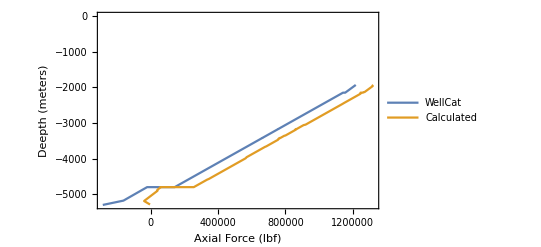

```mathematica
tablePi=Table[{VecPi[[i]],L[[i]]},{i,1,Length[L]}];
tablePe=Table[{VecPe[[i]],L[[i]]},{i,1,Length[L]}];
tableTi=Table[{Ti[[i]],L[[i]]},{i,1,Length[L]}];
tableTp=Table[{Tp[[i]],L[[i]]},{i,1,Length[L]}];
n=10;
PiData=ExpandTable[tablePi,n]; 
PeData=ExpandTable[tablePe,n];
TiData=ExpandTable[tableTi,n];
TpData=ExpandTable[tableTp,n];
Lcement=4803;
Ltotal=5303;
LDA=1933;
weigth=0;
young=3 10^7;
weigthperfeet=115;
di=12.376;
de=14;
nu=0.3;
pipedata={de,di,young,nu,weigthperfeet};
pipedatavec={
{14,12.376,young,nu,115,2150,5303,125000},
{13.625,12.376,young,nu,88.2,1933,2150,110000}
};
ax=ComputeAxialStress[PiData,PeData,pipedatavec,Lcement,Ltotal,TiData,TpData];
newax=InvertOrder[ax];

ListLinePlot[{stress,newax},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Axial Force (lbf)",""}},PlotLegends->{"WellCat","Calculated"}]
```

```mathematica
newax
```

{{-264333.,-5290.83},{-250801.,-5278.7},{-237270.,-5266.56},{-223738.,-5254.42},{-210206.,-5242.28},{-196674.,-5230.15},{-183143.,-5218.01},{-169611.,-5205.87},{-156079.,-5193.74},{-135628.,-5181.6},{-121124.,-5151.12},{-106621.,-5120.64},{-92116.7,-5090.16},{-77612.8,-5059.68},{-63108.9,-5029.2},{-48605.1,-4998.72},{-34101.2,-4968.24},{-19597.3,-4937.76},{-5093.46,-4907.28},{695.577,-4876.8},{4205.66,-4869.42},{7715.73,-4862.05},{11225.8,-4854.67},{14735.9,-4847.3},{18246.,-4839.92},{21756.,-4832.54},{25266.1,-4825.17},{28776.2,-4817.79},{31931.7,-4810.42},{32684.2,-4803.98},{32723.9,-4803.88},{32763.6,-4803.78},{32803.4,-4803.68},{32843.1,-4803.58},{32882.9,-4803.48},{32922.6,-4803.38},{32962.3,-4803.28},{33002.1,-4803.18},{33041.8,-4803.08},{231673.,-4802.98},{240385.,-4779.88},{249098.,-4756.78},{257810.,-4733.69},{266523.,-4710.59},{275236.,-4687.49},{283948.,-4664.39},{292661.,-4641.29},{301373.,-4618.2},{310086.,-4595.1},{321583.,-4572.},{333080.,-4541.52},{344577.,-4511.04},{356074.,-4480.56},{367571.,-4450.08},{379068.,-4419.6},{390565.,-4389.12},{402062.,-4358.64},{413559.,-4328.16},{425056.,-4297.68},{436553.,-4267.2},{448051.,-4236.72},{459548.,-4206.24},{471045.,-4175.76},{482542.,-4145.28},{494039.,-4114.8},{505536.,-4084.32},{517033.,-4053.84},{528530.,-4023.36},{540027.,-3992.88},{545775.,-3962.4},{551524.,-3947.16},{557273.,-3931.92},{563021.,-3916.68},{568770.,-3901.44},{574518.,-3886.2},{580267.,-3870.96},{586015.,-3855.72},{591764.,-3840.48},{597512.,-3825.24},{603261.,-3810.},{609009.,-3794.76},{614758.,-3779.52},{620506.,-3764.28},{626255.,-3749.04},{632003.,-3733.8},{637752.,-3718.56},{643500.,-3703.32},{649249.,-3688.08},{654998.,-3672.84},{662828.,-3657.6},{670659.,-3636.84},{678490.,-3616.08},{686320.,-3595.32},{694151.,-3574.56},{701982.,-3553.8},{709812.,-3533.04},{717643.,-3512.28},{725474.,-3491.52},{733304.,-3470.76},{734322.,-3450.},{735339.,-3447.3},{736356.,-3444.61},{737373.,-3441.91},{738391.,-3439.21},{739408.,-3436.52},{740425.,-3433.82},{741443.,-3431.12},{742460.,-3428.42},{743127.,-3425.73},{743164.,-3423.96},{743202.,-3423.86},{743240.,-3423.76},{743277.,-3423.66},{743315.,-3423.56},{743353.,-3423.46},{743391.,-3423.36},{743428.,-3423.26},{743172.,-3423.16},{743210.,-3423.84},{743247.,-3423.74},{743285.,-3423.64},{743323.,-3423.54},{743360.,-3423.44},{743398.,-3423.34},{743436.,-3423.24},{743474.,-3423.14},{743511.,-3423.04},{743549.,-3422.94},{746191.,-3422.84},{748833.,-3415.84},{751475.,-3408.83},{754117.,-3401.83},{756759.,-3394.82},{759400.,-3387.82},{762042.,-3380.82},{764684.,-3373.81},{767326.,-3366.81},{769968.,-3359.8},{776749.,-3352.8},{783530.,-3334.82},{790311.,-3316.85},{797092.,-3298.87},{803873.,-3280.89},{810654.,-3262.91},{817435.,-3244.94},{824215.,-3226.96},{830996.,-3208.98},{837423.,-3191.01},{837460.,-3173.97},{837498.,-3173.87},{837536.,-3173.77},{837574.,-3173.67},{837611.,-3173.57},{837649.,-3173.47},{837687.,-3173.37},{837725.,-3173.27},{837762.,-3173.17},{837800.,-3173.07},{842514.,-3172.97},{847228.,-3160.47},{851942.,-3147.98},{856655.,-3135.48},{861369.,-3122.98},{866083.,-3110.48},{870797.,-3097.99},{875511.,-3085.49},{880225.,-3072.99},{884939.,-3060.5},{896436.,-3048.},{907933.,-3017.52},{919430.,-2987.04},{930927.,-2956.56},{942424.,-2926.08},{953921.,-2895.6},{965418.,-2865.12},{976915.,-2834.64},{988412.,-2804.16},{999909.,-2773.68},{1.01141×10^6,-2743.2},{1.0229×10^6,-2712.72},{1.0344×10^6,-2682.24},{1.0459×10^6,-2651.76},{1.05739×10^6,-2621.28},{1.06889×10^6,-2590.8},{1.08039×10^6,-2560.32},{1.09189×10^6,-2529.84},{1.10338×10^6,-2499.36},{1.11488×10^6,-2468.88},{1.12576×10^6,-2438.4},{1.13663×10^6,-2409.56},{1.14751×10^6,-2380.73},{1.15839×10^6,-2351.89},{1.16927×10^6,-2323.05},{1.18014×10^6,-2294.22},{1.19102×10^6,-2265.38},{1.2019×10^6,-2236.54},{1.21278×10^6,-2207.7},{1.2233×10^6,-2178.87},{1.22334×10^6,-2150.97},{1.22337×10^6,-2150.87},{1.22341×10^6,-2150.77},{1.22345×10^6,-2150.67},{1.22349×10^6,-2150.57},{1.22352×10^6,-2150.47},{1.22356×10^6,-2150.37},{1.2236×10^6,-2150.27},{1.22364×10^6,-2150.17},{1.22368×10^6,-2150.07},{1.23736×10^6,-2149.97},{1.23784×10^6,-2148.33},{1.23831×10^6,-2146.7},{1.23878×10^6,-2145.06},{1.23926×10^6,-2143.42},{1.23973×10^6,-2141.79},{1.2402×10^6,-2140.15},{1.24068×10^6,-2138.51},{1.24115×10^6,-2136.87},{1.24162×10^6,-2135.24},{1.24702×10^6,-2133.6},{1.25242×10^6,-2114.94},{1.25782×10^6,-2096.29},{1.26321×10^6,-2077.63},{1.26861×10^6,-2058.97},{1.27401×10^6,-2040.31},{1.27941×10^6,-2021.66},{1.2848×10^6,-2003.},{1.2902×10^6,-1984.34},{1.29533×10^6,-1965.69},{1.29536×10^6,-1947.97},{1.29538×10^6,-1947.87},{1.29541×10^6,-1947.77},{1.29544×10^6,-1947.67},{1.29547×10^6,-1947.57},{1.2955×10^6,-1947.47},{1.29553×10^6,-1947.37},{1.29556×10^6,-1947.27},{1.29559×10^6,-1947.17},{1.29562×10^6,-1947.07},{1.29602×10^6,-1946.97},{1.29642×10^6,-1945.58},{1.29682×10^6,-1944.18},{1.29723×10^6,-1942.79},{1.29763×10^6,-1941.4},{1.29803×10^6,-1940.01},{1.29844×10^6,-1938.61},{1.29884×10^6,-1937.22},{1.29924×10^6,-1935.83},{1.29924×10^6,-1935.83}}

```mathematica
F=1.063 10^6-259000-10021
L=3.28(Lcement-LDA)
delta=(F/L)L^2/(2 young As)
young delta/L As
```

793979.

9413.6

3.70279

396990.

```mathematica
ComputeFballoning[12.376,14,9071.47,7330.850,0.3]
```

22342.1

```mathematica
ComputeBalooningFreePart[pipedatavec,PiData,PeData,Lcement]
```

-258016.

```mathematica
ComputePistonForce[PiData,PeData,pipedatavec]
```

-10212.

```mathematica
ComputeAxialReaction[WeigthFreePart-bal-PistonForceJoints,Pi/4 (de^2-di^2),3.28(4803-1933)]
```

396337.

```mathematica
Pi/4 (de^2-di^2)
```

33.6422

```mathematica
pipedatavec
```

{{14,12.376,30000000,0.3,115,2150,5303,125000},{13.625,12.376,30000000,0.3,88.2,1933,2150,110000}}

```mathematica
de
```

14

```mathematica
di
```

12.376

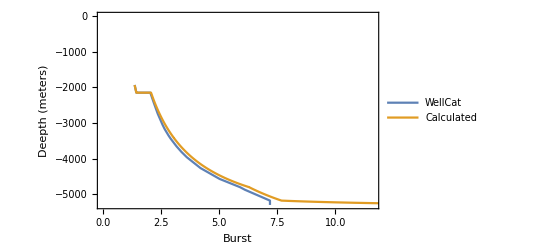

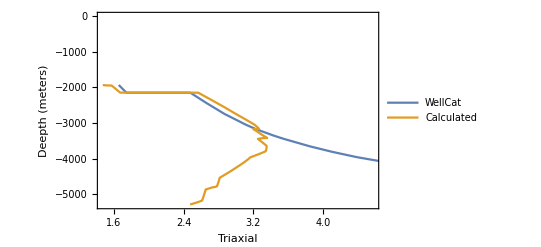

```mathematica
{barlowsf,apisf,vmsf}=ComputeSafetyFactors[pipedatavec,newax,PiData,PeData];
ListLinePlot[{burstSFvec,barlowsf},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Burst",""}},PlotLegends->{"WellCat","Calculated"}]
ListLinePlot[{triaxialSFvec,vmsf},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Triaxial",""}},PlotLegends->{"WellCat","Calculated"}]
```

```mathematica
b
```

b

First Cement Step

di = 12.376

de= 14

Mean[VecPicement] = 2529.15

Mean[VecPecement] = 11870.9

BalloningForce = 913886.

PistonForce = -1.59969×10^6

WeigthForce = 0

Last Cement Step

BalloningForce = 881187.

PistonForce = -1.59969×10^6

WeigthForce = 0.

First Free Step

Mean[VecPicement] = 288.792

Mean[VecPecement] = 6541.87

PistonForceJoints = -31366.1

BalloningForce = 583381.

WeigthFreePart = 1.06349×10^6

ReactionForce = 403876.

BalloningForce+PistonForceJoints+WeigthFreePart = 1.6155×10^6

WeigthForce = 1.0626×10^6

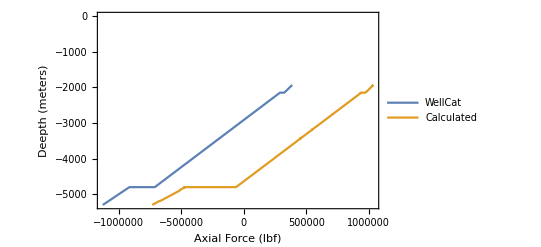

```mathematica
L={1933.04,1946.97,1947.03,2133.60,2149.97,2150.03,2438.40,2743.20,3048.00,3172.97,3173.03,3352.80,3422.84,3422.96,3423.03,3450.00,3657.60,3810.00,3962.40,4267.20,4572.00,4802.98,4803.04,4876.80,5181.60,5302.97};
AxialStress={387740,383688,383688,329692,324946,290064,181252,66252,-48748,-95909,-95909,-163748,-190176,-190234,-190234,-200421,-278748,-336248,-393748,-508748,-623748,-710903,-913884,-945470,-1074942,-1126742};
VecPi={3.29,3.32,3.32,3.64,3.66,3.66,4.16,4.68,5.19,5.41,5.41,5.71,5.83,5.83,5.83,5.88,274.68,534.40,794.15,1313.65,1833.10,2226.73,2226.83,2352.62,2872.05,3078.95};
VecPe={3854.56,3882.36,3882.48,4254.52,4287.16,4287.28,4862.32,5470.12,6077.92,6327.12,6327.24,6685.72,6825.40,6827.56,6828.65,7307.20,7926.40,8380.96,8835.52,9744.64,10653.76,11342.67,11342.85,11562.89,12472.01,12834.01};
Ti={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
Tp={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
(*Tp=Table[197,{i,1,Length[Tp]}];*)
stress=Table[{AxialStress[[i]],-L[[i]]},{i,1,Length[L]}];
tablePi=Table[{VecPi[[i]],L[[i]]},{i,1,Length[L]}];

tablePe=Table[{VecPe[[i]],L[[i]]},{i,1,Length[L]}];
tableTi=Table[{Ti[[i]],L[[i]]},{i,1,Length[L]}];
tableTp=Table[{Tp[[i]],L[[i]]},{i,1,Length[L]}];
n=100;
PiData=ExpandTable[tablePi,n];
PeData=ExpandTable[tablePe,n];
TiData=ExpandTable[tableTi,n];
TpData=ExpandTable[tableTp,n];
Lcement=4803;
Ltotal=5303;
weigth=0;
young=3 10^7;
weigthperfeet=115;
di=12.376;
de=14;
nu=0.3;
pipedata={de,di,young,nu,weigthperfeet};
pipedatavec={
{14,12.376,young,nu,115,2150,5303,125000},
{13.625,12.375,young,nu,88.2,1933,2150,110000}
};
ax=ComputeAxialStress[PiData,PeData,pipedatavec,Lcement,Ltotal,TiData,TpData];
newax=InvertOrder[ax];
ListLinePlot[{stress,newax},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Axial Force (lbf)",""}},PlotLegends->{"WellCat","Calculated"}]
```

```mathematica
stress
```

{{387740,-1933.04},{383688,-1946.97},{383688,-1947.03},{329692,-2133.6},{324946,-2149.97},{290064,-2150.03},{181252,-2438.4},{66252,-2743.2},{-48748,-3048.},{-95909,-3172.97},{-95909,-3173.03},{-163748,-3352.8},{-190176,-3422.84},{-190234,-3422.96},{-190234,-3423.03},{-200421,-3450.},{-278748,-3657.6},{-336248,-3810.},{-393748,-3962.4},{-508748,-4267.2},{-623748,-4572.},{-710903,-4802.98},{-913884,-4803.04},{-945470,-4876.8},{-1074942,-5181.6},{-1126742,-5302.97}}

```mathematica
alpha=12.42 10^-6
e=3 10^7;
```

0.00001242

```mathematica
de
```

14

Interpolation::inddp: The point 3.52 in dimension 1 is duplicated.

Interpolation[{{3.39,1933.18},{3.49,1933.32},{3.59,1933.46},{3.69,1933.6},{3.79,1933.74},{3.89,1933.88},{3.99,1934.02},{4.09,1934.15},{4.19,1934.29},{4.29,1934.43},2464,{3060.33,5292.05},{3062.4,5293.26},{3064.47,5294.47},{3066.54,5295.69},{3068.6,5296.9},{3070.67,5298.12},{3072.74,5299.33},{3074.81,5300.54},{3076.88,5301.76},{3078.95,5302.97}}]
 |  |  |  |

InterpolatingFunction[{{3854.84, 12834.}}, <>]

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

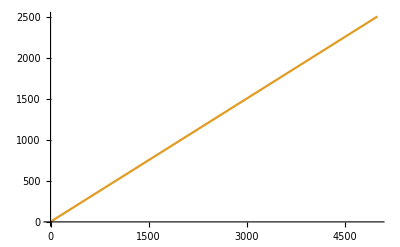

```mathematica
pi=Interpolation[PiData]
pe=Interpolation[PeData]
Plot[{pi[x],pe[x]},{x,0,5000}]
```

```mathematica
pi[2]
```

Interpolation[{{3.39,1933.18},{3.49,1933.32},{3.59,1933.46},{3.69,1933.6},{3.79,1933.74},{3.89,1933.88},{3.99,1934.02},{4.09,1934.15},{4.19,1934.29},{4.29,1934.43},{4.39,1934.57},2463,{3060.33,5292.05},{3062.4,5293.26},{3064.47,5294.47},{3066.54,5295.69},{3068.6,5296.9},{3070.67,5298.12},{3072.74,5299.33},{3074.81,5300.54},{3076.88,5301.76},{3078.95,5302.97}}][2]
 |  |  |  |

```mathematica
sigr
```

(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2))

```mathematica
sigr[2]
```

(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2))[2]

```mathematica
A
```

222231.

```mathematica
Clear[h,sigr,sigt]
sigr[h_]:=(pi[h] (r^2-re^2) ri^2+pe[h] re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
sigt[h_]:=(pi[h](r^2+re^2) ri^2-pe[h] re^2 (r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
subst={r->ri,nu->0.30,PI->3078.95,PO->12834.01,ri->di/2,re->de/2,Young->3 10^7,alpha->12.42 10^-6 };
Aext=Pi re^2;
Aint=Pi ri^2;
As=Aext-Aint;
As=As//.subst;
sol1=NIntegrate[-(nu(sigr[h]+sigt[h])As)//.subst,{h,Lcement,Ltotal}]

VecPicement=FilterData[PiData,Lcement,0];
VecPecement=FilterData[PeData,Lcement,0];
PIM=Mean[VecPicement];
POM=Mean[VecPecement];
Sr=(PIM (r^2-re^2) ri^2+POM re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
St=(PIM(r^2+re^2) ri^2-POM re^2 (r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
subst={r->ri,nu->0.30,PI->3078.95,PO->12834.01,ri->di/2,re->de/2,Young->3 10^7,alpha->12.42 10^-6 };
d=(Aext-Aint)(PO-PI )/.subst
e=(Aext-Aint)(PO )/.subst
sol2=(nu(Sr+St)As-d)//.subst
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{4803,4804.82}}.

NIntegrate[-(nu (sigr[h]+sigt[h]) As)//.subst,{h,Lcement,Ltotal}]

328182.

431765.

-1.24207×10^6

```mathematica
FilterData[PiData,Lcement,1]
```

{3.39,3.49,3.59,3.69,3.79,3.89,3.99,4.09,4.19,4.29,4.39,4.49,4.59,4.69,4.79,4.89,4.99,5.09,5.19,5.29,5.39,5.49,5.59,5.69,5.79,5.89,5.99,6.09,6.19,6.29,6.39,6.49,6.59,6.69,6.79,6.89,6.99,7.09,7.19,7.29,7.39,7.49,7.59,7.69,7.79,7.89,7.99,8.09,8.19,8.29,8.39,8.49,8.59,8.69,8.79,8.89,8.99,9.09,9.19,9.29,9.39,9.49,9.59,9.69,9.79,9.89,9.99,10.09,10.19,10.29,10.39,10.49,10.59,10.69,10.79,10.89,10.99,11.09,11.19,11.29,11.39,11.49,11.59,11.69,11.79,11.89,11.99,12.09,12.19,12.29,12.39,12.49,12.59,12.69,12.79,12.89,12.99,13.09,13.19,13.29,3.52,3.62,3.72,3.82,3.92,4.02,4.12,4.22,4.32,4.42,4.52,4.62,4.72,4.82,4.92,5.02,5.12,5.22,5.32,5.42,5.52,5.62,5.72,5.82,5.92,6.02,6.12,6.22,6.32,6.42,6.52,6.62,6.72,6.82,6.92,7.02,7.12,7.22,7.32,7.42,7.52,7.62,7.72,7.82,7.92,8.02,8.12,8.22,8.32,8.42,8.52,8.62,8.72,8.82,8.92,9.02,9.12,9.22,9.32,9.42,9.52,9.62,9.72,9.82,9.92,10.02,10.12,10.22,10.32,10.42,10.52,10.62,10.72,10.82,10.92,11.02,11.12,11.22,11.32,11.42,11.52,11.62,11.72,11.82,11.92,12.02,12.12,12.22,12.32,12.42,12.52,12.62,12.72,12.82,12.92,13.02,13.12,13.22,13.32,3.52,3.62,3.72,3.82,3.92,4.02,4.12,4.22,4.32,4.42,4.52,4.62,4.72,4.82,4.92,5.02,5.12,5.22,5.32,5.42,5.52,5.62,5.72,5.82,5.92,6.02,6.12,6.22,6.32,6.42,6.52,6.62,6.72,6.82,6.92,7.02,7.12,7.22,7.32,7.42,7.52,7.62,7.72,7.82,7.92,8.02,8.12,8.22,8.32,8.42,8.52,8.62,8.72,8.82,8.92,9.02,9.12,9.22,9.32,9.42,9.52,9.62,9.72,9.82,9.92,10.02,10.12,10.22,10.32,10.42,10.52,10.62,10.72,10.82,10.92,11.02,11.12,11.22,11.32,11.42,11.52,11.62,11.72,11.82,11.92,12.02,12.12,12.22,12.32,12.42,12.52,12.62,12.72,12.82,12.92,13.02,13.12,13.22,13.32,3.84,3.94,4.04,4.14,4.24,4.34,4.44,4.54,4.64,4.74,4.84,4.94,5.04,5.14,5.24,5.34,5.44,5.54,5.64,5.74,5.84,5.94,6.04,6.14,6.24,6.34,6.44,6.54,6.64,6.74,6.84,6.94,7.04,7.14,7.24,7.34,7.44,7.54,7.64,7.74,7.84,7.94,8.04,8.14,8.24,8.34,8.44,8.54,8.64,8.74,8.84,8.94,9.04,9.14,9.24,9.34,9.44,9.54,9.64,9.74,9.84,9.94,10.04,10.14,10.24,10.34,10.44,10.54,10.64,10.74,10.84,10.94,11.04,11.14,11.24,11.34,11.44,11.54,11.64,11.74,11.84,11.94,12.04,12.14,12.24,12.34,12.44,12.54,12.64,12.74,12.84,12.94,13.04,13.14,13.24,13.34,13.44,13.54,13.64,3.86,3.96,4.06,4.16,4.26,4.36,4.46,4.56,4.66,4.76,4.86,4.96,5.06,5.16,5.26,5.36,5.46,5.56,5.66,5.76,5.86,5.96,6.06,6.16,6.26,6.36,6.46,6.56,6.66,6.76,6.86,6.96,7.06,7.16,7.26,7.36,7.46,7.56,7.66,7.76,7.86,7.96,8.06,8.16,8.26,8.36,8.46,8.56,8.66,8.76,8.86,8.96,9.06,9.16,9.26,9.36,9.46,9.56,9.66,9.76,9.86,9.96,10.06,10.16,10.26,10.36,10.46,10.56,10.66,10.76,10.86,10.96,11.06,11.16,11.26,11.36,11.46,11.56,11.66,11.76,11.86,11.96,12.06,12.16,12.26,12.36,12.46,12.56,12.66,12.76,12.86,12.96,13.06,13.16,13.26,13.36,13.46,13.56,13.66,3.86,3.96,4.06,4.16,4.26,4.36,4.46,4.56,4.66,4.76,4.86,4.96,5.06,5.16,5.26,5.36,5.46,5.56,5.66,5.76,5.86,5.96,6.06,6.16,6.26,6.36,6.46,6.56,6.66,6.76,6.86,6.96,7.06,7.16,7.26,7.36,7.46,7.56,7.66,7.76,7.86,7.96,8.06,8.16,8.26,8.36,8.46,8.56,8.66,8.76,8.86,8.96,9.06,9.16,9.26,9.36,9.46,9.56,9.66,9.76,9.86,9.96,10.06,10.16,10.26,10.36,10.46,10.56,10.66,10.76,10.86,10.96,11.06,11.16,11.26,11.36,11.46,11.56,11.66,11.76,11.86,11.96,12.06,12.16,12.26,12.36,12.46,12.56,12.66,12.76,12.86,12.96,13.06,13.16,13.26,13.36,13.46,13.56,13.66,4.36,4.46,4.56,4.66,4.76,4.86,4.96,5.06,5.16,5.26,5.36,5.46,5.56,5.66,5.76,5.86,5.96,6.06,6.16,6.26,6.36,6.46,6.56,6.66,6.76,6.86,6.96,7.06,7.16,7.26,7.36,7.46,7.56,7.66,7.76,7.86,7.96,8.06,8.16,8.26,8.36,8.46,8.56,8.66,8.76,8.86,8.96,9.06,9.16,9.26,9.36,9.46,9.56,9.66,9.76,9.86,9.96,10.06,10.16,10.26,10.36,10.46,10.56,10.66,10.76,10.86,10.96,11.06,11.16,11.26,11.36,11.46,11.56,11.66,11.76,11.86,11.96,12.06,12.16,12.26,12.36,12.46,12.56,12.66,12.76,12.86,12.96,13.06,13.16,13.26,13.36,13.46,13.56,13.66,13.76,13.86,13.96,14.06,14.16,4.88,4.98,5.08,5.18,5.28,5.38,5.48,5.58,5.68,5.78,5.88,5.98,6.08,6.18,6.28,6.38,6.48,6.58,6.68,6.78,6.88,6.98,7.08,7.18,7.28,7.38,7.48,7.58,7.68,7.78,7.88,7.98,8.08,8.18,8.28,8.38,8.48,8.58,8.68,8.78,8.88,8.98,9.08,9.18,9.28,9.38,9.48,9.58,9.68,9.78,9.88,9.98,10.08,10.18,10.28,10.38,10.48,10.58,10.68,10.78,10.88,10.98,11.08,11.18,11.28,11.38,11.48,11.58,11.68,11.78,11.88,11.98,12.08,12.18,12.28,12.38,12.48,12.58,12.68,12.78,12.88,12.98,13.08,13.18,13.28,13.38,13.48,13.58,13.68,13.78,13.88,13.98,14.08,14.18,14.28,14.38,14.48,14.58,14.68,5.39,5.49,5.59,5.69,5.79,5.89,5.99,6.09,6.19,6.29,6.39,6.49,6.59,6.69,6.79,6.89,6.99,7.09,7.19,7.29,7.39,7.49,7.59,7.69,7.79,7.89,7.99,8.09,8.19,8.29,8.39,8.49,8.59,8.69,8.79,8.89,8.99,9.09,9.19,9.29,9.39,9.49,9.59,9.69,9.79,9.89,9.99,10.09,10.19,10.29,10.39,10.49,10.59,10.69,10.79,10.89,10.99,11.09,11.19,11.29,11.39,11.49,11.59,11.69,11.79,11.89,11.99,12.09,12.19,12.29,12.39,12.49,12.59,12.69,12.79,12.89,12.99,13.09,13.19,13.29,13.39,13.49,13.59,13.69,13.79,13.89,13.99,14.09,14.19,14.29,14.39,14.49,14.59,14.69,14.79,14.89,14.99,15.09,15.19,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91,15.01,15.11,15.21,15.31,15.41,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91,15.01,15.11,15.21,15.31,15.41,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91,15.01,15.11,15.21,15.31,15.41,15.51,15.61,15.71,6.03,6.13,6.23,6.33,6.43,6.53,6.63,6.73,6.83,6.93,7.03,7.13,7.23,7.33,7.43,7.53,7.63,7.73,7.83,7.93,8.03,8.13,8.23,8.33,8.43,8.53,8.63,8.73,8.83,8.93,9.03,9.13,9.23,9.33,9.43,9.53,9.63,9.73,9.83,9.93,10.03,10.13,10.23,10.33,10.43,10.53,10.63,10.73,10.83,10.93,11.03,11.13,11.23,11.33,11.43,11.53,11.63,11.73,11.83,11.93,12.03,12.13,12.23,12.33,12.43,12.53,12.63,12.73,12.83,12.93,13.03,13.13,13.23,13.33,13.43,13.53,13.63,13.73,13.83,13.93,14.03,14.13,14.23,14.33,14.43,14.53,14.63,14.73,14.83,14.93,15.03,15.13,15.23,15.33,15.43,15.53,15.63,15.73,15.83,6.03,6.13,6.23,6.33,6.43,6.53,6.63,6.73,6.83,6.93,7.03,7.13,7.23,7.33,7.43,7.53,7.63,7.73,7.83,7.93,8.03,8.13,8.23,8.33,8.43,8.53,8.63,8.73,8.83,8.93,9.03,9.13,9.23,9.33,9.43,9.53,9.63,9.73,9.83,9.93,10.03,10.13,10.23,10.33,10.43,10.53,10.63,10.73,10.83,10.93,11.03,11.13,11.23,11.33,11.43,11.53,11.63,11.73,11.83,11.93,12.03,12.13,12.23,12.33,12.43,12.53,12.63,12.73,12.83,12.93,13.03,13.13,13.23,13.33,13.43,13.53,13.63,13.73,13.83,13.93,14.03,14.13,14.23,14.33,14.43,14.53,14.63,14.73,14.83,14.93,15.03,15.13,15.23,15.33,15.43,15.53,15.63,15.73,15.83,6.03,6.13,6.23,6.33,6.43,6.53,6.63,6.73,6.83,6.93,7.03,7.13,7.23,7.33,7.43,7.53,7.63,7.73,7.83,7.93,8.03,8.13,8.23,8.33,8.43,8.53,8.63,8.73,8.83,8.93,9.03,9.13,9.23,9.33,9.43,9.53,9.63,9.73,9.83,9.93,10.03,10.13,10.23,10.33,10.43,10.53,10.63,10.73,10.83,10.93,11.03,11.13,11.23,11.33,11.43,11.53,11.63,11.73,11.83,11.93,12.03,12.13,12.23,12.33,12.43,12.53,12.63,12.73,12.83,12.93,13.03,13.13,13.23,13.33,13.43,13.53,13.63,13.73,13.83,13.93,14.03,14.13,14.23,14.33,14.43,14.53,14.63,14.73,14.83,14.93,15.03,15.13,15.23,15.33,15.43,15.53,15.63,15.73,15.83,11.256,13.944,16.632,19.32,22.008,24.696,27.384,30.072,32.76,35.448,38.136,40.824,43.512,46.2,48.888,51.576,54.264,56.952,59.64,62.328,65.016,67.704,70.392,73.08,75.768,78.456,81.144,83.832,86.52,89.208,91.896,94.584,97.272,99.96,102.648,105.336,108.024,110.712,113.4,116.088,118.776,121.464,124.152,126.84,129.528,132.216,134.904,137.592,140.28,142.968,145.656,148.344,151.032,153.72,156.408,159.096,161.784,164.472,167.16,169.848,172.536,175.224,177.912,180.6,183.288,185.976,188.664,191.352,194.04,196.728,199.416,202.104,204.792,207.48,210.168,212.856,215.544,218.232,220.92,223.608,226.296,228.984,231.672,234.36,237.048,239.736,242.424,245.112,247.8,250.488,253.176,255.864,258.552,261.24,263.928,266.616,269.304,271.992,274.68,277.277,279.874,282.472,285.069,287.666,290.263,292.86,295.458,298.055,300.652,303.249,305.846,308.444,311.041,313.638,316.235,318.832,321.43,324.027,326.624,329.221,331.818,334.416,337.013,339.61,342.207,344.804,347.402,349.999,352.596,355.193,357.79,360.388,362.985,365.582,368.179,370.776,373.374,375.971,378.568,381.165,383.762,386.36,388.957,391.554,394.151,396.748,399.346,401.943,404.54,407.137,409.734,412.332,414.929,417.526,420.123,422.72,425.318,427.915,430.512,433.109,435.706,438.304,440.901,443.498,446.095,448.692,451.29,453.887,456.484,459.081,461.678,464.276,466.873,469.47,472.067,474.664,477.262,479.859,482.456,485.053,487.65,490.248,492.845,495.442,498.039,500.636,503.234,505.831,508.428,511.025,513.622,516.22,518.817,521.414,524.011,526.608,529.206,531.803,534.4,536.998,539.595,542.192,544.79,547.387,549.985,552.582,555.18,557.777,560.375,562.972,565.57,568.167,570.765,573.362,575.96,578.557,581.155,583.752,586.35,588.947,591.545,594.142,596.74,599.337,601.935,604.532,607.13,609.727,612.325,614.922,617.52,620.117,622.715,625.312,627.91,630.507,633.105,635.702,638.3,640.897,643.495,646.092,648.69,651.287,653.885,656.482,659.08,661.677,664.275,666.872,669.47,672.067,674.665,677.262,679.86,682.457,685.055,687.652,690.25,692.847,695.445,698.042,700.64,703.237,705.835,708.432,711.03,713.627,716.225,718.822,721.42,724.017,726.615,729.212,731.81,734.407,737.005,739.602,742.2,744.797,747.395,749.992,752.59,755.187,757.785,760.382,762.98,765.577,768.175,770.772,773.37,775.967,778.565,781.162,783.76,786.357,788.955,791.552,794.15,799.345,804.54,809.735,814.93,820.125,825.32,830.515,835.71,840.905,846.1,851.295,856.49,861.685,866.88,872.075,877.27,882.465,887.66,892.855,898.05,903.245,908.44,913.635,918.83,924.025,929.22,934.415,939.61,944.805,950.,955.195,960.39,965.585,970.78,975.975,981.17,986.365,991.56,996.755,1001.95,1007.15,1012.34,1017.54,1022.73,1027.93,1033.12,1038.32,1043.51,1048.71,1053.9,1059.1,1064.29,1069.49,1074.68,1079.88,1085.07,1090.27,1095.46,1100.66,1105.85,1111.05,1116.24,1121.44,1126.63,1131.83,1137.02,1142.22,1147.41,1152.61,1157.8,1163.,1168.19,1173.39,1178.58,1183.78,1188.97,1194.17,1199.36,1204.56,1209.75,1214.95,1220.14,1225.33,1230.53,1235.72,1240.92,1246.11,1251.31,1256.5,1261.7,1266.89,1272.09,1277.28,1282.48,1287.67,1292.87,1298.06,1303.26,1308.45,1313.65,1318.84,1324.04,1329.23,1334.43,1339.62,1344.82,1350.01,1355.21,1360.4,1365.6,1370.79,1375.98,1381.18,1386.37,1391.57,1396.76,1401.96,1407.15,1412.35,1417.54,1422.73,1427.93,1433.12,1438.32,1443.51,1448.71,1453.9,1459.1,1464.29,1469.49,1474.68,1479.87,1485.07,1490.26,1495.46,1500.65,1505.85,1511.04,1516.24,1521.43,1526.62,1531.82,1537.01,1542.21,1547.4,1552.6,1557.79,1562.99,1568.18,1573.38,1578.57,1583.76,1588.96,1594.15,1599.35,1604.54,1609.74,1614.93,1620.13,1625.32,1630.51,1635.71,1640.9,1646.1,1651.29,1656.49,1661.68,1666.88,1672.07,1677.27,1682.46,1687.65,1692.85,1698.04,1703.24,1708.43,1713.63,1718.82,1724.02,1729.21,1734.4,1739.6,1744.79,1749.99,1755.18,1760.38,1765.57,1770.77,1775.96,1781.16,1786.35,1791.54,1796.74,1801.93,1807.13,1812.32,1817.52,1822.71,1827.91,1833.1,1837.04,1840.97,1844.91,1848.85,1852.78,1856.72,1860.65,1864.59,1868.53,1872.46,1876.4,1880.34,1884.27,1888.21,1892.14,1896.08,1900.02,1903.95,1907.89,1911.83,1915.76,1919.7,1923.63,1927.57,1931.51,1935.44,1939.38,1943.32,1947.25,1951.19,1955.13,1959.06,1963.,1966.93,1970.87,1974.81,1978.74,1982.68,1986.62,1990.55,1994.49,1998.42,2002.36,2006.3,2010.23,2014.17,2018.11,2022.04,2025.98,2029.92,2033.85,2037.79,2041.72,2045.66,2049.6,2053.53,2057.47,2061.41,2065.34,2069.28,2073.21,2077.15,2081.09,2085.02,2088.96,2092.9,2096.83,2100.77,2104.7,2108.64,2112.58,2116.51,2120.45,2124.39,2128.32,2132.26,2136.2,2140.13,2144.07,2148.,2151.94,2155.88,2159.81,2163.75,2167.69,2171.62,2175.56,2179.49,2183.43,2187.37,2191.3,2195.24,2199.18,2203.11,2207.05,2210.98,2214.92,2218.86,2222.79,2226.73}

```mathematica
(nu(sigr[Lcement]+sigt[Lcement])As)
(nu(sigr[Ltotal]+sigt[Ltotal])As)
```

10.0927 (0.00243873 (0.-410.049 Interpolation[{{3.39,1933.18},{3.49,1933.32},{3.59,1933.46},{3.69,1933.6},{3.79,1933.74},{3.89,1933.88},{3.99,1934.02},{4.09,1934.15},{4.19,1934.29},2467,{3064.47,5294.47},{3066.54,5295.69},{3068.6,5296.9},{3070.67,5298.12},{3072.74,5299.33},{3074.81,5300.54},{3076.88,5301.76},{3078.95,5302.97}}][4803])+0.00243873 (-9.03859×10^6+1))
 |  |  |  |

10.0927 (0.00243873 (0.-410.049 Interpolation[{{3.39,1933.18},{3.49,1933.32},{3.59,1933.46},{3.69,1933.6},{3.79,1933.74},{3.89,1933.88},{3.99,1934.02},{4.09,1934.15},{4.19,1934.29},2467,{3064.47,5294.47},{3066.54,5295.69},{3068.6,5296.9},{3070.67,5298.12},{3072.74,5299.33},{3074.81,5300.54},{3076.88,5301.76},{3078.95,5302.97}}][5303])+0.00243873 (-9.97951×10^6+1))
 |  |  |  |

```mathematica
A
```

222231.

```mathematica
Clear[nu,sigr,sigt,e,alpha,Fax]
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigt=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));Unprotect[C]

d=(Aext-Aint)(PO-PI )/.subst
e=(Aext-Aint)(PO )/.subst
C=Young alpha 0 (Aext-Aint)/.subst
Faxs=Solve[A+B+C==Fax,Fax]//Expand
```

{}

328182.

431765.

0

{{Fax→222231.}}

```mathematica
A-d
B+e
B+d
```

-105951.

431765.

328182.

```mathematica
90.29-114.814
```

-24.524

```mathematica
Solve[-2.568412121996958*^6+12535.096768235991 dt==-1126742,dt]
```

{{dt→115.011}}

```mathematica
Solve[TP-90.29==115,TP]
```

{{TP→205.29}}

```mathematica
Faxs//FullSimplify
```

{{Fax→222231.}}

```mathematica
Expand[(-re+ri) (re+ri)]
```

-re^2+ri^2

```mathematica
Clear[nu,sigr,sigt,e,alpha,Fax]
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigt=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
Aext=Pi re^2;
Aint=Pi ri^2;
Unprotect[C]
subst={r->ri,nu->0.30,PI->3078.95,PO->12834.01,ri->di/2,re->de/2,Young->3 10^7,alpha->12.42 10^-6 };
A=2nu PI Aint//.subst
B=0/.subst
C=Young alpha dt (Aext-Aint)/.subst
Faxs=Solve[A+B-C==Fax,Fax]//Expand
Faxs/.{nu->0.30,PI->3078.95,PO->12834.01,ri->de/2,re->de/2}
Faxs
Faxs/.{nu->0.30,PI->3078.95,PO->0,ri->di/2,re->de/2}
```

{}

222231.

0

12535.1 dt

{{Fax→222231.-12535.1 dt}}

{{Fax→222231.-12535.1 dt}}

{{Fax→222231.-12535.1 dt}}

«1 more identical outputs»

```mathematica
Solve[222230.86129482018-12535.096768235991 dt==-1126742,dt]
```

{{dt→107.616}}

```mathematica
Solve[TP-90.29==107.616,TP]
```

{{TP→197.906}}

```mathematica
(*ComputePistonForce[PiData_,PeData_,PipeData_]:=Block[{i,olddi,oldde,pipe,de,di,young,nu,weigthperfeet,L1,L2,PistonForce=0,sigy},
pipe=1;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
For[i=Length[PipeData],i>1,i--,
olddi=di;
oldde=de;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
(*PistonForce-=Pi/4 (de^2-di^2) PiData[[i,1]];*)
PistonForce-=Pi/4 (olddi^2-di^2) PiData[[i,1]]-Pi/4 (oldde^2-de^2) PeData[[i,1]];
];
PistonForce
];*)
```

```mathematica
(*ComputeAxialStress[PiData_,PeData_,PipeData_,Lcement_,Ltotal_,Ti_,Tp_]:=Block[{de,di,young,nu,weigthperfeet,BalloningForce=0,PistonForce=0,TemperatureForce=0,WeigthForce=0,dh=0,AxialForce={},ReactionForce=0,MeanPiFree=0,MeanPeFree=0,VecPi,VecPe,i,L1,L2,olddi,pipe,oldde,MeanTiFree,MeanTpFree,VecTi,VecTp,PistonForceJoints,sigy},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
pipe=1;
For[i=Length[PiData],i>1,i--,
(*No primeiro passo calcula o efeito pistão de fundo*)
If[i==Length[PiData],
PistonForce=-Pi/4 de^2 PeData[[i,1]]+ Pi/4 di^2 PiData[[i,1]];

Print["PeData[[i,1]] = ",PeData[[i,1]]];
Print["PiData[[i,1]] = ",PiData[[i,1]]];
Print["PistonForce = ",PistonForce];
];

(*mudanca de tubular e aplicação do efeito pistão*)
If[L1>PiData[[i,2]],
olddi=di;
oldde=de;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
(*PistonForce-=Pi/4 (olddi^2-di^2) PiData[[i,1]]-Pi/4 (oldde^2-de^2) PeData[[i,1]];*)
PistonForce=Pi/4 (de^2-di^2) PiData[[i,1]];
];

If[PiData[[i,2]]>=Lcement,
(*Trecho Cimentado*)
BalloningForce=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];
TemperatureForce=ComputeFtemperature[de,di,(Ti[[i,1]]+Ti[[i-1,1]])/2,(Tp[[i,1]]+Tp[[i-1,1]])/2];
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;
AppendTo[AxialForce,{-BalloningForce+PistonForce+WeigthForce+TemperatureForce,-PiData[[i,2]]}];
WeigthForce+=weigthperfeet dh;
flag=True;
,
(*Trecho Livre*)
If[flag==True,
VecPi=FilterData[PiData,Lcement];
VecPe=FilterData[PeData,Lcement];
VecTi=FilterData[Ti,Lcement];
VecTp=FilterData[Tp,Lcement];
MeanPiFree=Mean[VecPi];(*Media da pressão interna no trecho livre*)
MeanPeFree=Mean[VecPe];(*Media da pressão externa no trecho livre*)
MeanTiFree=Mean[VecTi];(*Media da temperatura inicial  no trecho livre*)
MeanTpFree=Mean[VecTp];(*Media da temperatura na produção no trecho livre*)
BalloningForce=ComputeFballoning[di,de,MeanPiFree,MeanPeFree,nu];(*Efeito Balão Trecho Livre*)
TemperatureForce=ComputeFtemperature[de,di,MeanTiFree,MeanTpFree];(*Efeito Temperatura Trecho Livre*)
PistonForceJoints=ComputePistonForce[PiData,PeData,PipeData];(*Efeito Pistão Mudança de Tubulares Trecho Livre*)
ReactionForce=ComputeAxialReaction[BalloningForce+TemperatureForce+PistonForceJoints ,de,di];(*Reação Interface Cimento*)
];
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;
AppendTo[AxialForce,{-ReactionForce+WeigthForce+PistonForce,-PiData[[i,2]]}];
WeigthForce+=weigthperfeet dh;
flag=False;
];
];
AxialForce
];*)
```

Part::partd: Part specification {{9182.9,5204.03},{9183.35,5205.03},{9183.8,5206.03},{9184.25,5207.03},{9184.7,5208.03},{9185.15,5209.03},{9185.6,5210.03},{9186.05,5211.03},{9186.5,5212.02},{9186.95,5213.02},{9187.4,5214.02},«30»,{9201.34,5245.},{9201.79,5246.},{9202.24,5247.},{9202.69,5248.},{9203.14,5249.},{9203.59,5250.},{9204.04,5251.},{9204.49,5252.},{9204.93,5253.},«449»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{9135.16,5204.03},{9136.58,5205.03},{9138.,5206.03},{9139.42,5207.03},{9140.83,5208.03},{9142.25,5209.03},{9143.67,5210.03},{9145.09,5211.03},{9146.51,5212.02},{9147.93,5213.02},{9149.35,5214.02},«30»,{9193.33,5245.},{9194.75,5246.},{9196.17,5247.},{9197.59,5248.},{9199.,5249.},{9200.42,5250.},{9201.84,5251.},{9203.26,5252.},{9204.68,5253.},«449»}⟦0,2⟧ is longer than depth of object.

First Cement Step

di = 8.539

de= 9.875

Mean[VecPicement] = 9308.67

Mean[VecPecement] = 9529.8

BalloningForce = 118077.

PistonForce = -225953.

WeigthForce = 0

WeigthForce = 276015.

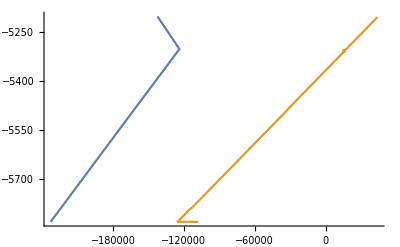

```mathematica
Pint={9182.45,9227.42,9227.44,9309.95,9447.09,9465.89};
Pext={9133.74,9275.62,9275.71,9536.04,9968.76,10028.06};
AxialForce={-142314,-123739,-123739,-161605,-224146,-232808};
Ti={93.83,90.29,90.29,97.44,109.31,110.94};
Tp={93.83,90.29,90.29,97.44,109.31,110.94};
L={5203.03,5302.97,5303.03,5486.40,5791.20,5832.96};
stress=Table[{AxialForce[[i]],-L[[i]]},{i,1,Length[L]}];

tablePi=Table[{Pint[[i]],L[[i]]},{i,1,Length[L]}];
tablePe=Table[{Pext[[i]],L[[i]]},{i,1,Length[L]}];
tableTi=Table[{Ti[[i]],L[[i]]},{i,1,Length[L]}];
tableTp=Table[{Tp[[i]],L[[i]]},{i,1,Length[L]}];
n=100;
PiData=ExpandTable[tablePi,n];
PeData=ExpandTable[tablePe,n];
TiData=ExpandTable[tableTi,n];
TpData=ExpandTable[tableTp,n];

Lcement=5203;
Ltotal=5832;
young=3 10^7;
nu=0.3;
pipedatavec={
{9.875,8.539,young,nu,66.9,5203,5832,125000}
};
ax=ComputeAxialStress[PiData,PeData,pipedatavec,Lcement,Ltotal,TiData,TpData];
ListLinePlot[{stress,ax},PlotRange->All]
```